```mathematica
palindrome8[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,y],z]],ColorFunction->"DarkBands",Background->White]
```

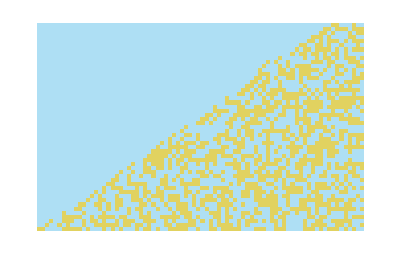

```mathematica
palindrome8[196,50,2]
```

```mathematica
rep[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#]+#]]])&,x,y],z]],Color]
```

```mathematica
repgraph[x_Integer,y_Integer]:=NestGraph[(FromDigits[Sort[IntegerDigits[IntegerReverse[#]+#]]])&,x,y,VertexLabels->"Name"]
```